```mathematica
(*Data[i_]:=Import[FileNameJoin[{NotebookDirectory[],"L="<>ToString@i<>",P=(08,12),n=10000PLANE,EM2.out"}]]
Data2[i_]:=Import[FileNameJoin[{NotebookDirectory[],"L="<>ToString@i<>",P=(08,12),n=100PLANE,EM2(test).out"}]]
EM2Data[i_]:=Import[FileNameJoin[{NotebookDirectory[],"L="<>ToString@i<>",P=(04,08),n=10000PLANE,EM2.out"}]]
testData:=Import[FileNameJoin[{NotebookDirectory[],"test1.out"}]]*)
testData:=normalizeData[Import[FileNameJoin[{NotebookDirectory[],"test.out"}]],1000]
nolossData:=normalizeData[Import[FileNameJoin[{NotebookDirectory[],"noloss.out"}]],1000]
```

```mathematica
normalizeData[data_,n_]:=Drop[data,1]/.{{a_,b_,c_,d_}:>{a,b,c,(1-d/n)//N},{}->Nothing};
```

```mathematica
(*Indep noise*)
```

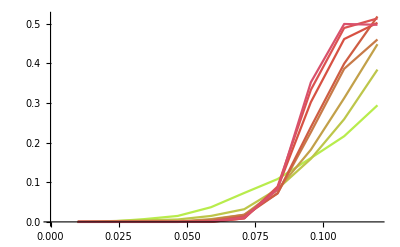

```mathematica
ListLinePlot[Map[#[[{2,4}]]&,Values@GroupBy[testData,First],{2}],PlotStyle->Table[ColorData["NeonColors"][i],{i,0,1,0.1}]]
```

```mathematica
(**)
```

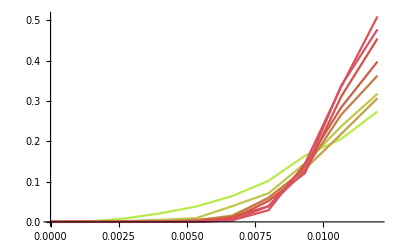

```mathematica
ListLinePlot[Map[#[[{2,4}]]&,Values@GroupBy[nolossData,First],{2}],PlotStyle->Table[ColorData["NeonColors"][i],{i,0,1,0.1}]]
```